## HW 9: Transit of an Extrasolar Planet

While FITS files can hold a an image,  they very often holds other types of data instead of images or in addition to images. The data stored in the FITS file you will be working with is time series data from the Kepler spacecraft. These data contain the lightcurve for a transiting extra-solar planet. A transit is when a planet passes between us and its host star and block a portion of the light coming from the star. Your job is to use a Fourier Transform to determine the period of the transiting planet and then phase fold the lightcurve such that we can get a very clean graph of a planetary transit.

## 1. Locate files and read “Metadata”

The file we will be working with kplr011446443-2009259160929_llc.fits
Import[] the “Metadata” and store result in variable metaData
Look at metadata using Flatten[] and TableForm[]
Evaluate the following
	“TFIELDS”/.metaData
	“TTYPE1”/. metaData
	“TTYPE4”/. metaData
	“TTYPE8”/. metaData
	“RA_OBJ”/. metaData
	“DEC_OBJ”/. metaData
	“TELESCOP”/. metaData
	“INSTRUME”/. metaData

```mathematica
SetDirectory[NotebookDirectory[]];
FileNames["011446443\\*.fits"];
metaData = Import[%[[3]],"Metadata"];
metaData[[2]]//TableForm;
"TFIELDS"/.metaData
"TTYPE1"/. metaData
"TTYPE4"/. metaData
"TTYPE8"/. metaData
"RA_OBJ"/. metaData
"DEC_OBJ"/. metaData
"TELESCOP"/. metaData
"INSTRUME"/. metaData
```

{TFIELDS,{20,number of table fields},TFIELDS}

{TTYPE1,{TIME,column title: data time stamps},TTYPE1}

{TTYPE4,{SAP_FLUX,column title: aperture photometry flux},TTYPE4}

{TTYPE8,{PDCSAP_FLUX,column title: aperture phot. PDC flux},TTYPE8}

{{286.808,[deg] right ascension},{286.808,[deg] right ascension},{286.808,[deg] right ascension}}

{{49.3164,[deg] declination},{49.3164,[deg] declination},{49.3164,[deg] declination}}

{{Kepler,telescope},{Kepler,telescope},{Kepler,telescope}}

{{Kepler Photometer,detector type},{Kepler Photometer,detector type},{Kepler Photometer,detector type}}

## 2. Import the Data

Import[] the “Data” and store the result in a variable named “data”
Take a look at Dimensions[] of the data

ListPlot[], with Joined→True, TTYPE1 (column 1 of data) versus TTYPE4 (column 4 of data) which is flux versus time.
(Note: you will need to use Transpose[] to get the time, flux pairs that you need)

Zoom in to a few days of data, using PlotRange[]and show points using Mesh→All, to look at a single planetary transit.

{4354,20}

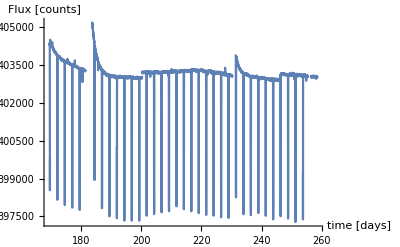

```mathematica
FileNames["011446443\\*.fits"];
data= Import[%[[3]], "Data"][[1]];
Dimensions[data]
ListPlot[{data[[All,1]], data[[All,4]]}//Transpose, PlotRange-> {All,All},Joined-> True,AxesLabel->{"time [days]","Flux [counts]"}]
```

## 3. Repeat with PDCSAP_FLUX

Repeat the steps in Part 2 wit the PDCSAP_FLUX. Use the outputs from Part 1 to locate the PDCSAP_FLUX (i.e. which column of “data” must be selected).

From the Kepler FAQ:

“The PDCSAP light curve is the flux contained in the optimal aperture in electrons per second after the PDC module has applied its detrending algorithm to the PA light curve. Readers should also consult the target pixel file FAQ”

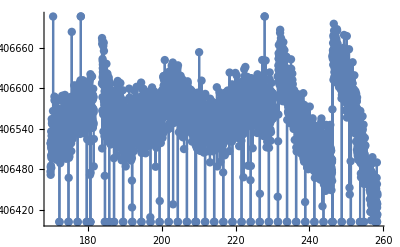

```mathematica
ListPlot[{data[[All,1]], data[[All,8]]}//Transpose,Joined-> True,Mesh-> All]
```

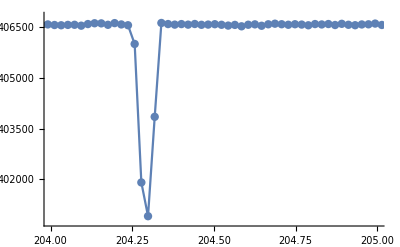

```mathematica
ListPlot[{data[[All,1]], data[[All,8]]}//Transpose, PlotRange-> {{204,205},All},Joined-> True,Mesh-> All]
```

```mathematica
ListPlot[{data[[All,1]],
 data[[All,10]]}//Transpose, PlotRange-> All,Joined-> True]
```

## 4. Take Fourier Transform

Remove Indeterminate values by replacing them with previous numeric value. Once you have performed the Fourier Transform, plot the power spectrum (absolute value of transform) using ListPlot[].

Simple hack provided:

```mathematica
nd =data[[All,8]]; (* produces a padded array, "nd" to be used in the Foruier Transform.*)
If[nd[[1]]===Indeterminate,nd[[1]]= 406000]
Table[
If[nd[[i]]===Indeterminate, 
nd[[i]] = nd[[i-1]]
]
,{i ,1, Length[nd]}
];
```

406000

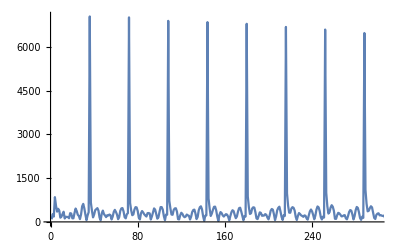

```mathematica
Abs[Fourier[nd]];
ListPlot[%[[2;;All]],PlotRange-> {{0,300},All},Joined-> True]
```

## 5. Create Frequency list for Fourier data

If you remember back to our lab on Fourier Transforms, we needed to create a list of data the contain the frequencies output from the Fourier Transform. We can then use this list of frequencies as our x-axis. The frequencies will range from 0, 1/t_total, 2/t_total, ..., (Length[nd]-2)/t_total, (Length[nd]-1)/t_total, where t_total is the total elapsed time of the data set.

```mathematica
data[[All,1]][[1]];
data[[All,1]][[-1]];
tTotal = %-%%
fVals = 1/%Range[0,Length[nd]-1];
Dimensions[nd]==Dimensions[fVals]
```

88.9473

True

## 6. Create Power Spectrum Plot to Find the Period

Find the frequency of the first peak (other than the DC offset at f = 0) and invert that frequency to find the period of the planet.

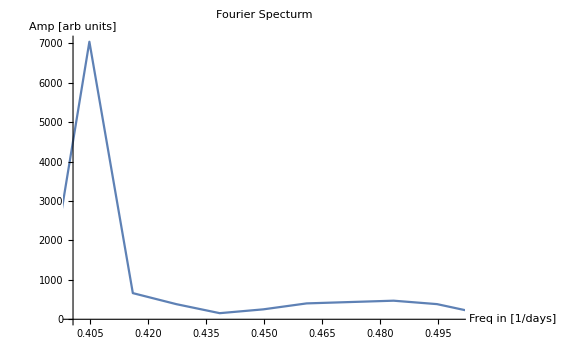

{{0.337278,617.394},{0.348521,465.716},{0.359764,248.691},{0.371006,58.8534},{0.382249,222.188},{0.393491,333.903},{0.404734,7040.53},{0.415977,663.356},{0.427219,383.78},{0.438462,154.81},{0.449705,251.482}}

7040.53

Period of Planet is 2.47076 days

```mathematica
Abs[Fourier[nd]];
fd = {fVals[[2;;All]],%[[2;;All]]}//Transpose;
ListPlot[%,PlotRange-> {{0.4,0.5},All},Joined-> True,ImageSize->Large,
PlotLabel-> "Fourier Specturm",
AxesLabel-> {"Freq in [1/days]","Amp [arb units]"}
]
fd[[30;;40]]
%[[7,2]]
Framed["Period of Planet is "<> ToString[1/%%[[7,1]]]<> " days"]
```

## 7. Refining the Period

The frequency resolution of teh Fourier Transform is limited by the length of the data set. Thus, we can “Pad” the data in order to improve frequency resolution. This will to increase accuracy of the orbital period calculation. Padding the data is a term used to describe a method of lengthening the data set by simply adding a bunch of numbers to the end of it. In this case, we will be adding 200,000 copies of the last data point to the end of the data set. Create a new data set “padData”, by joining a list with 200,00 copies of the final data point to the original data set, “nd”.  Once you have your new data set “padData”, repeat Parts 5 & 6 to determine the period of the planet.

```mathematica
tTotal
Length[nd]
padData = Join[nd,ConstantArray[nd[[-1]],200000]];
ampPad = Abs[Fourier[padData]];
tTotalPad = tTotal(Length[ampPad]-1)/(Length[nd]-1)
fPad = 1/tTotalPad Range[0,Length[ampPad]-1];
Length[fPad] == Length[ampPad] == Length[padData]
fdPad = {fPad[[2;;All]],ampPad[[2;;All]]}//Transpose;
```

88.9473

4354

4175.66

True

```mathematica
ListPlot[fdPad,PlotRange-> {{0.3,.5},All},Joined-> True,ImageSize->Large,
PlotLabel-> "Fourier Specturm",
AxesLabel-> {"Freq in [1/days]","Amp [arb units]"}
]
```

-Graphics-

```mathematica
FindPeaks[fdPad[[All,2]],0,0,600];
fdPad[[%[[1,1]],1]];
 Subscript[T, orbit]=1/%
Framed["From padded FFT, T_orbit= " <> ToString[Subscript[T, orbit]] <> " days"]
Subscript[T, orbit]//FullForm
```

2.4708

From padded FFT, T_orbit= 2.4708 days

2.4708

## 8. Fold the Flux data using the period

Use Mod[] to fold the data. That is to say we need to slice the data up into pieces that are the length of the period. You will create a new 2-dimensional list, where the x values will just be copies of the time from 0 - T, and the y values will be the data slices. We can then use ListPlot[] to see a very nice single transit of the planet.

2.4708

2.4706

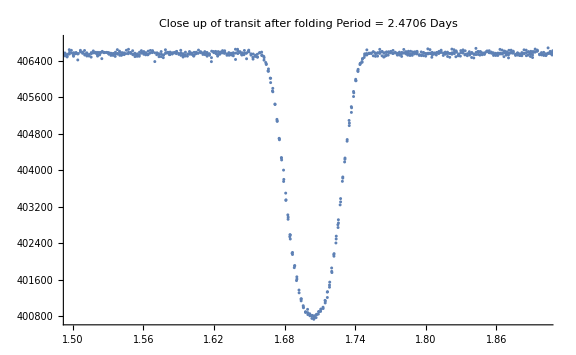

```mathematica
tt = Subscript[T, orbit]
tt=2.4706
endPoint=All;
ListPlot[{Map[Mod[#,tt]&,data[[1;;endPoint,1]]], data[[1;;endPoint,8]]}//Transpose, Mesh->All, Joined-> False,PlotRange-> {{1.5,1.9},All},
PlotLabel-> "Close up of transit after folding\nPeriod = " <>ToString[tt] <> " Days",
ImageSize-> Large
]
```